```mathematica
OS="linux";(*or linux*)
Needs["ErrorBarPlots`"]
Needs["EDA`"]
<<PhysicalConstants`
ch=PlanckConstant/(Joule Second);
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\nedm-analysis\\analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/nedm-analysis/analysis"]];
Print["(faster) Rawdata Directory:",fasDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
runNum=10288;
maxCy=231;
posCycles=Table[k,{k,9,56}];
zeroCycles=Join[Table[k,{k,1,8}],Table[k,{k,57,64}]];
negCycles=Table[k,{k,65,112}];
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory:/home/prajwal/Dropbox/nEDM/nedm-analysis/analysis

(faster) Rawdata Directory:/home/prajwal/nEDM/rawdata

(ASCII) Rawdata Directory:/home/prajwal/Dropbox/nEDM/rawdata

```mathematica
data=0;
posasym=Table[0,{k,1,maxCy}];
negasym=Table[0,{k,1,maxCy}];
posup=Table[0,{k,1,maxCy}];posdown=Table[0,{k,1,maxCy}];negup=Table[0,{k,1,maxCy}];negdown=Table[0,{k,1,maxCy}];
zeroup=Table[0,{k,1,maxCy}];
zerodown=Table[0,{k,1,maxCy}];
For[i=1,i≤maxCy,i++,
data = ReadList[StringJoin[AscDir,"/",IntegerString[runNum,10,6],"/",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[i,10,3],"_0001.fast.ascii"],{Real,Word,Real,Real,Real,Real,Real}];
For[j=1,j≤Dimensions[data][[1]],j++,
If[((data[[j]][[3]]==1||data[[j]][[3]]==2||data[[j]][[3]]==3||data[[j]][[3]]==5||data[[j]][[3]]==6||data[[j]][[3]]==7||data[[j]][[3]]==8||data[[j]][[3]]==9)&&(data[[j]][[6]]>=2000
))||((data[[j]][[3]]==4)&&(data[[j]][[6]]≥1500)),
If[MemberQ[posCycles,Mod[i,113]],
posup[[i]]++,
If[MemberQ[negCycles,Mod[i,113]],
negup[[i]]++,
If[MemberQ[zeroCycles,Mod[i,113]],
zeroup[[i]]++,
];
];
];
];
If[((data[[j]][[3]]==11||data[[j]][[3]]==12||data[[j]][[3]]==13||data[[j]][[3]]==14||data[[j]][[3]]==15||data[[j]][[3]]==16||data[[j]][[3]]==17||data[[j]][[3]]==18||data[[j]][[3]]==19)&&(data[[j]][[6]]≥2500
)),,
If[MemberQ[posCycles,Mod[i,113]],
posdown[[i]]++,
If[MemberQ[negCycles,Mod[i,113]],
negdown[[i]]++,
If[MemberQ[zeroCycles,Mod[i,113]],
zerodown[[i]]++,
];
];
];
];
];
(*Print["Cycle # ",i," : +U=",posup[[i]],", -U=",negup[[i]],", oU=",zeroup[[i]],", -D=",negdown[[i]],", +D=",posdown[[i]],", oD=",zerodown[[i]]];*)
];
```

ReadList::readn: Invalid real number found when reading from "/home/prajwal/Dropbox/nEDM/rawdata/010288/010288_UCNdet_019_0001.fast.ascii".

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReadList::readn: Invalid real number found when reading from "/home/prajwal/Dropbox/nEDM/rawdata/010288/010288_UCNdet_108_0001.fast.ascii".

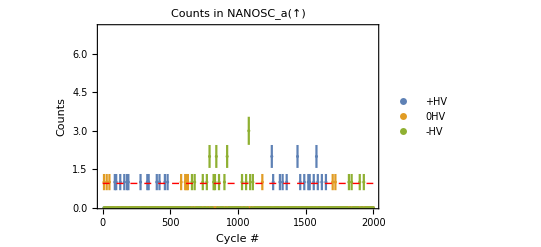

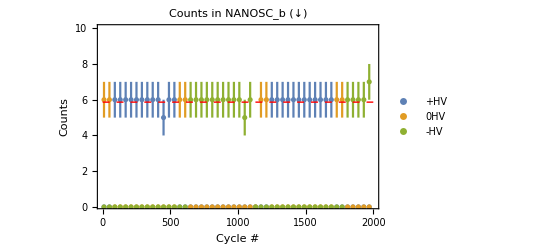

```mathematica
lineStyle1={Thin,Red,Dashed};
ptn1=Table[{10k,{posup[[k]],√(posup[[k]]/10)}},{k,1,200}];
ptn2=Table[{10k,{zeroup[[k]],√(zeroup[[k]]/10)}},{k,1,200}];
ptn3=Table[{10k,{negup[[k]],√(negup[[k]]/10)}},{k,1,200}];
line21=Line[{{0,Mean[3posup]+Mean[3zeroup]+Mean[3negup]},{2000,Mean[3posup]+Mean[3zeroup]+Mean[3negup]}}];
EDAListPlot[ptn1,ptn2,ptn3,Epilog->{Directive[lineStyle1],line21},Frame->True,FrameLabel->{Style["Cycle #",FontSize->18],Style["Counts",FontSize->18]},TicksStyle->Large,PlotLabel->Style["Counts in NANOSC_a(↑)",FontSize->18],PlotLegends->{"+HV","0HV","-HV"},PlotRange->{{1,2000},{0.1,7}},LabelStyle->{18}]
ptn4=Table[{10k,{Round[posdown[[k]]/100],Sqrt[Round[posdown[[k]]/1000]]}},{k,1,200,4}];
ptn5=Table[{10k,{Round[zerodown[[k]]/100],Sqrt[Round[zerodown[[k]]/1000]]}},{k,1,200,4}];
ptn6=Table[{10k,{Round[negdown[[k]]/100],Sqrt[Round[negdown[[k]]/1000]]}},{k,1,200,4}];
line22=Line[{{0,(Mean[posdown]+Mean[zerodown]+Mean[negdown])/100},{2000,(Mean[posdown]+Mean[zerodown]+Mean[negdown])/100}}];
EDAListPlot[ptn4,ptn5,ptn6,Epilog->{Directive[lineStyle1],line22},Frame->True,FrameLabel->{Style["Cycle #",FontSize->18],Style["Counts",FontSize->18]},TicksStyle->Large,PlotLabel->Style["Counts in NANOSC_b (↓)",FontSize->18],PlotLegends->{"+HV","0HV","-HV"},PlotRange->{{1,2000},{0.1,10}},LabelStyle->{18}]
```

{0.00003,0.00028}

{3.06429×10^-27,2.86×10^-26}

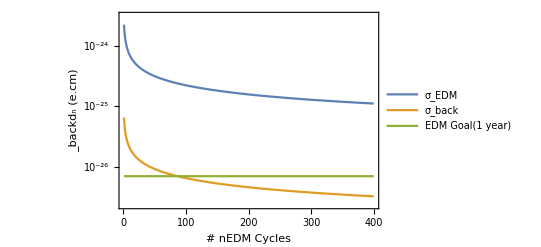

```mathematica
sposup={Total[posup],Sqrt[Total[posup]]};
sposdown={Total[posdown],Sqrt[Total[posdown]]};
snegup={Total[negup],Sqrt[Total[negup]]};
snegdown={Total[negdown],Sqrt[Total[negdown]]};
asympos=CombineWithError[(sposup-sposdown)/(sposup+sposdown)];
asymneg=CombineWithError[(snegup-snegdown)/(snegup+snegdown)];
deltaasym=Abs[CombineWithError[asympos-asymneg]]
bkdn=(deltaasym 1.4 11×10^-22 6.5)/(14 7)/1000
LogPlot[{1.4*^-25×√250 / Sqrt[t],bkdn[[2]]×Sqrt[300/58] / Sqrt[t],7*^-27},{t,1,400},Frame->True,FrameLabel->{"# nEDM Cycles","_backd_n (e.cm)"},PlotLegends->{"σ_EDM","σ_back","EDM Goal(1 year)"},LabelStyle->{18}]
```

```mathematica
N[(Mean[posdown]+Mean[zerodown]+Mean[negdown])/1000]
```

0.586519

```mathematica
{3.064285714285714*^-27,2.8599999999999994*^-26}/30^2
```

{3.40476×10^-30,3.17778×10^-29}